# The Dynamics Workbench Documentation Notebook Copyright © 1994-2014 Arthur D. Kuo

The Dynamics Workbench is a Mathematica package for doing dynamics. It enables the user to generate equations of motion primarily for rigid body mechanical systems. These equations may then be exported for use in other programs, or may be integrated directly in Mathematica. The Workbench provides just a few basic commands which are sufficient for generating equations of motion. Lower level commands give advanced users access to a the actual steps involved, but are not necessary in the majority of cases. This package uses Kane's method to generate equations, but can be used to implement the method of Lagrange as well.

## How to Get Started

To begin learning to use the Dynamics Workbench, read the sections below up to and including Basic Commands. Skip the sections on Intermediate and Lower Level Commands, and proceed directly to the example. At this point you are ready to try your own models. Refer back to the sections you skipped if you require more information.

## Initialization

Load the Dynamics Workbench package using a command like the following:

```mathematica
Needs["DynamicsWorkbench`"]
```

You must configure your system so that the package DynamicsWorkbench.m is in Mathematica's path.

## Configuration

### Bodies and Frames

The Dynamics Workbench describes a mechanical system using body's and reference frame's. One or more  body's may be used to describe a rigid body to be modeled, and one or more reference frame's may be attached to that body. Most often, there will be a single body and reference frame associated with a rigid body.

body's are organized relative to each other in the description of a system. Each body is defined with respect to an inboard body which precedes it. These two body's are connected by a joint, of which there are many types. The Dynamics Workbench requires information regarding the location of that joint relative to both body's. On body, the vector BodyToJnt describes the joint location with respect to body's center of mass. On the inboard body, the vector InbToJnt describes the joint location with respect to inboard's center of mass. The figure below illustrates these vectors and the two bodies with their joints separated.

The Dynamics Workbench uses reference frame's to describe vectors fixed to certain body's. Each body generally has one or more frame's fixed to it. Any point fixed to a body can be described using any of these frame's. Associated with a frame is a set of three mutually-orthogonal unit vectors, labeled with names of the form frame[i] where i takes on value 1, 2, or 3.

There is a single default body and associated frame defined in the Dynamics Workbench, corresponding to the Newtonian reference frame and called ground. All additional body's and frame's are defined relative to ground, using a variety of joint types to describe the kinematic relationship.

## Notation

The Dynamics Workbench uses a very simple notation for refering to generalized coordinates, vectors, and reference frames.

### Generalized coordinates and speeds

Generalized coordinates are referred to as q[n], and generalized speeds as u[n]. Both of these variables are implicitly functions of time.

### Vectors in reference frames

A reference frame named, for example, a, will generally be fixed to a body also named a, which will have axes a[1], a[2], a[3]. These axes will be aligned respectively with the axes of the inboard body, when the generalized coordinates for a are set to zero. Thus, a vector in reference frame a might be 0.5 a[1] + 0.3 a[2].

### Dyadics

A dyadic is expressed using the ** symbol, which normally signifies NonCommutativeMultiply. In this case, the dyadic is not commutative, and is of the form I11 a[1]**a[1] + I12 a[1]**a[2] + I22 a[2]**a[2] + I33 a[3]**a[3].

## Basic Commands

### NewModel

The command NewModel[] is used to clear the internal variables storing parameters of a model.

#### Example

```mathematica
NewModel[]
```

### AddBody

AddBody[ new_body, inboard_body, joint_type ] adds a body, new_body, which is attached to the previously-defined inboard_body with a joint specified by joint_type. After a call to NewModel[], the only existing body is ground, the Newtonian reference frame. Currently supported joint types are Hinge, Slider, UJoint, Ball, and SixDOF (see section on joints). The output of AddBody is a list of two lists containing the generalized coordinates and generalized speeds for the new body.

#### Options

BodyToJnt->0 | bodytojoint is the vector, specified in any reference frame or frames, from the new body’s center of mass to the joint connecting it to the inboard body.

InbToJnt->0 | inboardtojoint is the vector, specified in any reference frame or frames, from the inboard body's center of mass to the joint connecting it to the new body.

Mass-> 0 | mass is the mass of the new body.

Inertia-> 0 | inertia is the central inertia dyadic of the new body. There are three possible forms for this dyadic: a full dyadic representation such as I12 a[1]**a[2]; an inertia matrix for the body's reference frame; and a list of the diagonal entries of that matrix, if the reference frame's axes are principal axes.

Qdof->Automatic | qdof_# is the number to be given to the generalized coordinate for the new degree of freedom. If Automatic, the Workbench automatically chooses a number. If the joint type has more than one generalized coordinate, these are named Qdof1, Qdof2,...

Udof->Automatic | udof_# is the number to be given to the generalized speed for the new degree of freedom. If Automatic, the Workbench automatically chooses a number. If the joint type has more than one degree of freedom, these are named Udof1, Udof2,...

RelativeTo->Automatic | body specifies the reference frame which the new reference frame is relative to. If Automatic, the inboard body's reference frame is used. It is common to use ground, so that the generalized coordinate for a hinge joint would be a segment angle.

Axis->{0,0,1} | dir_cos gives the axis of the joint using direction cosines in the new body's reference frame. Alternative expressions for Axis are the coordinate number (±1, ±2, ±3) with the sign signifying counter-clockwise (+) or clockwise (-) rotation, or a vector in the inboard body's reference frame. If the joint type has more than one axis, these are named Axis1, Axis2,…

TAxis->{0,0,1} | dir_cos gives the translational axis of the joint using direction cosines in the new body's reference frame, as used for Slider or SixDOF joints. Alternative expressions for TAxis are the coordinate number (±1, ±2, ±3) with the sign signifying movement measured in the positive or negative direction of the axis, or a vector in the inboard body's reference frame. If the joint type has more than one translational axis, these are named TAxis1, TAxis2,…

Frme->Automatic | frme_name sets the name of the reference frame which is fixed to the new body. By default, the frame is given the same name as the body.

Basefrm->Automatic | base_frame sets the reference frame which the new reference frame is relative to, as in RelativeTo. Options Frme and Basefrm are rarely necessary.

#### Joint Types

Fixed is a zero degree-of-freedom joint, in which the inboard and reference bodies do not move relative to each other. It is often used to perform a change of coordinates or to accomodate an unusual geometric arrangement of bodies. Its axes can be offset from those of the base reference frame using the Offset option. Offset may be a matrix of direction cosines or a list of vectors specifying the offset axes in terms of the base frame.  Examples: Offset-> {{0,1,0},{1,0,0},{0,0,1}}, Offset->{body[2],body[1],body[3]}. A Fixed joint has no generalized speeds or coordinates associated with it.

Hinge is a single degree-of-freedom rotatory joint. The axis about which the joint rotates is specified by the option Axis, which may be the coordinate number, a list of direction cosines, or a vector in the base reference frame (the frame of the inboard body). Examples: Axis->3, Axis->{0,0,1}, Axis->body[1]. The generalized speed, Udof, is defined to be the time-derivative of generalized coordinate Qdof.

Slider is a single degree-of-freedom prismatic joint. Its location and home position are specified by the BodyToJoint option. The slider joint is at a home position when its generalized coordinate has a value of zero. In this position, the joints for the inboard and outboard bodies are coincident. As the generalized coordinate changes in value, these two joints separate along a translational axis specified by TAxis, which may be a coordinate number, a list of direction cosines, or a vector in the base reference frame. Examples: TAxis->3, TAxis->{0,0,1}, TAxis->body[1]. The generalized speed, Udof, is defined to be the time-derivative of generalized coordinate Qdof.

UJoint is a two degree-of-freedom rotatory joint. Its home position is coincident with the base reference frame (the frame of the inboard body). The generalized coordinates describing the rotations are the successive rotation angles about the two specified rotation axes, Axis1 and Axis2. The generalized speeds, Udof1 and Udof2, are defined to be the time-derivatives of the respective generalized coordinates, Qdof1 and Qdof2.

Ball is a three degree-of-freedom rotatory joint with orientation described by euler parameters. Its home position is coincident with the base reference frame (the frame of the inboard body). The generalized coordinates Qdof1 through Qdof4 describing the rotations are in the form of euler parameters {e1,e2,e3,e4}, where e4 is the cosine of the half-rotational angle. Use Gimbal if different generalized coordinates are desired. The generalized speeds Udof1 through Udof3 are the angular velocities about the body's reference frame axes.

Gimbal is a three degree-of-freedom rotatory joint with orientation described by euler angles. Its home position is coincident with the base reference frame (the frame of the inboard body). The generalized coordinates describing the rotations are the successive rotation angles about the three specified rotation axes, described by options Axis1, Axis2, and Axis3. Use Ball if euler parameters are preferred as generalized coordinates. Axes may be specified by coordinate number, or a list of direction cosines. Examples: Axis1->3, Axis2->1, Axis3->2; Axis1->{0,0,1}, Axis2->{0,.707,.707}, Axis3->{.707,0,.707}.

SixDOF is a six degree-of- freedom joint which allows for full translational and rotational movement between bodies.  Its location ahd home position are specified by the BodyToJoint option. The translational axes are specified by TAxis1, TAxis2, and TAxis3. The translations along those axes are specified by generalized coordinates Qdof1, Qdof2, and Qdof3, and by generalized speeds Udof1, Udof2, and Udof3. The rotational orientation is described by four euler parameters, specified by generalized coordinates Qdof4 through Qdof7. The angular velocities about the base frame's axes are specified by generalized speeds Udof1, Udof2, and Udof3.

#### Example

```mathematica
AddBody[a,ground,Hinge]
```

{{1},{1}}

In this example, Qdof1 and Udof1 are not specified by the user. The Dynamics Workbench has automatically selected values of 1 for each.

### AppFrc

AppFrc[ body, force, point ] applies a force specified by vector force (in any reference frame or frames) at a point specified by vectorforce  (relative to the center of mass) of body.

#### Example

```mathematica
AppFrc[a,-ground[1],2 a[1]]
```

1

A force of magnitude 1 directed in the negative direction of the ground[1] axis, is applied to body a. The point of application is specified by the vector 2 a[1] from body a's center of mass.

### AppTrq

AppTrq[ body, torque ] applies a torque (or moment) specified by vector torque (in any reference frame or frames) to body.

#### Example

```mathematica
AppTrq[a,10 a[3]]
```

1

A torque of magnitude 10 directed in the  direction of the ground[3] axis, is applied to body a.

### EOM

The command EOM[] assembles equations of motion for the system with previously entered bodies, forces, and torques.

The command AtT0[ expr ] is used to set initial conditions by applying to an expression such as q[1] == 0, and making that expression valid for time zero.

### Kinematics

Kinematics returns the set of kinematical differential equations. The Dynamics Workbench usually uses equations q[n]'[t] == u[n][t], but the user may define arbitrary relationships, e.g., for complex kinematical joints.

## Intermediate Level Commands

The Dynamics Workbench provides several useful intermediate level commands, which are not required for formulation of equations of motion, but aid analysis or rearrangement of these equations.

### CollectE

The command CollectE[ equations ] collects together terms in eqequationsuations which are linear in the time-derivative of the generalized speeds, making the equations somewhat more readable.

The command CollectE[ equations, expr ] collects together terms in equations which are linear in expr, making the equations somewhat more readable.

### AddFrame

The command AddFrame[ frame, baseframe, jointtype, options ] adds a new reference frame to the system, just as AddBody, but without a body attached to the reference frame. This command is useful for defining custom joints or body configurations, by decoupling body specifications from reference frame specifications.

### AsmStateEqn

AsmStateEqn[ eom, kinematics ] assembles the state equations, using input arguments corresponding to the equations of motion and the kinematical differential equations. The resulting equations are differential equations in the generalized coordinates and speeds, and are suitable for use by RungeKutta.

### RHS

RHS[ eqns ] returns the right-hand-side of each equation in a list of equations.

### SolveEqn

SolveEqn[ eqn, vars ] rearranges a list of equations in terms of the variables vars. The command also sorts this list.

### MassMatrix

Given the equations of motion, MassMatrix[ eom ] provides a list of two outputs: the mass matrix (terms linear in the time-derivatives of generalized speeds u), and the right-hand side. These outputs can be used in the linear system M.udot == rhs, as when integrating the equations of motion.

### AtT0

AtT0[expr] returns expr set at time zero. This command is useful for providing initial conditions to NDSolve.

### FindEquil

FindEquil[ eqn, {x,x0} ] finds the equilibrium point in the given equation, for variable x. The initial guess of x0 is used to start a Newton search. For a list of equations, use FindEquil[ eqns, {x,x0}, {y,y0},...] to find equilibrium points in several variables x, y, etc.

### PosCOM

PosCOM[body] returns a vector describing the position of the center of mass of body with respect to the ground reference frame.

### PosPnt

PosPnt[point,body] returns the vector describing the position of point (entered as a vector relative to the center of mass) fixed to body.

### Tmtx

Tmtx[frame] is the transformation matrix which maps between frame and the inertial (ground) reference frame. Tmtx returns a list of coordinates of the three axes of frame, each in the form of a sublist comprising coefficients for axes of reference frame.

## Lower Level Commands

At the lowest level of simplification, the Dynamics Workbench provides routines which enable one to assemble equations of motion "by hand," save for the most basic mathematical operations. The Workbench makes it easy to manipulate vectors in various reference frames by providing a simple notation and framework for these operations.

### Accelerations

AccCOM[body] returns a vector describing the acceleration of the center of mass of body with respect to the ground reference frame.

AccJnt[body] returns the velocity of the point on the inboard body which corresponds to the location of the joint connecting the two.

AngAcc[body] returns the angular acceleration of the body with respect to ground.

### Velocities

AngVel[body] returns the angular velocity of the body with respect to ground.

VelCOM[body] returns a vector describing the velocity of the center of mass of body with respect to the ground reference frame.

VelJnt[body] returns the velocity of the point on the inboard body which corresponds to the location of the joint connecting the two.

VelJnt2[body] returns the velocity of the point on body which instantaneously corresponds to the location of the joint between body and the inboard body. Used in slider joints.

### Model Structure

Bodies returns a list of the currently defined bodies.

Force[body] returns a list of the forces acting on the body.

Frames returns a list of the currently defined reference frames.

Inboard[body] returns the name of the body inboard to the argument.

Inertia[body] is the inertia dyadic of the body.

Kids[frame] returns a list of reference frames below the argument's entry in the frame tree.

Mass[body] is the mass of the body.

Parents[frame] returns a list of reference frames above the argument's entry in the frame tree.

Torque[body] returns a list of the torques acting on the body.

### Kane's Method

PrtVel[expr,n] or PrtVel[expr,u[n]] returns the partial velocity of expression with respective to the nth generalized speed.

ResltF[body] returns the resultant of the forces acting on the body.

ResltT[body] returns the resultant of the torques or moments acting on the body.

Rstar[body] returns the inertia forces acting on body.

Tstar[body] returns the inertia torque acting on body.

GActFrc[body,n] returns the generalized active force of body with respect to the nth generalized speed. GActFrc[body] returns the generalized active forces for body with respect to each of the generalized speeds. GActFrc[All] returns the sum of the generalized active forces for all bodies, with respect to each of the generalized speeds.

GInerFrc[body,n] returns the generalized inertia force of body with respect to the nth generalized speed. GInerFrc[body] returns the generalized inertia forces for body with respect to each of the generalized speeds. GInerFrc[All] returns the sum of the generalized inertia forces for all bodies, with respect to each of the generalized speeds.

### Transformation between reference frames

CastMtx[from,to] returns the transformation
matrix needed to cast a vector from one reference frame to
another.

CastV[vector,frame] will cast any vector into a specified reference frame.

Tmtx[frame] is the transformation matrix which maps between frame and the inertial (ground) reference frame. Tmtx returns a list of coordinates of the three axes of frame, each in the form of a sublist comprising coefficients for axes of reference frame.

### Vector Operations

Cross[vector1,vector2] or (vector1 ~X~ vector2) performs the cross product of two vectors.

Dot[vector1,vector2] or vector1 . vector2 performs the dot product of two vectors (or a vector and a dyadic).

A dyadic may be performed by using vector1 ** vector2. The symbol ** denotes a noncommutative multiply within Mathematica, in accordance with the fact that dyadics are not commutative.

Dist[point1,point2] returns the distance between two points, which need not be described in the same reference frames.

## Example: Ballistic walker

This example is an analysis of ballistic walking, described by Mochon & McMahon (1980). Given the correct initial conditions, it is possible for a biped to walk one step with no external input. This ballistic motion resembles actual human walking to a surprising degree. The model consists of three segments, including a stance leg and the thigh and shank of the swing leg. Segments are joined by Hinge joints. All motion is planar.
Ref: Mochon & McMahon, J. Biomech. 13:49-57, 1980.

If you haven't already, be sure to load the Dynamics Workbench (but don't execute this command if the Workbench is already loaded):

```mathematica
Needs["DynamicsWorkbench`"]
```

Initialize variables by using this command:

```mathematica
NewModel[]
```

Add rigid bodies to the model by specifying a new body name, which is connected to the specified inboard body. Here we are attaching body a to ground with a Hinge joint. The central moment of inertia is specified in dyadic form. Vectors specify the location of the joint relative to the body's center of mass, and relative to the inboard body's center of mass. The axis of the hinge joint is also specified.

```mathematica
AddBody[a,ground,Hinge,Mass->M0,Inertia->I0 a[3]**a[3],BodyToJnt->(lc0-l0) a[2],InbToJnt->0,Axis->{0,0,1}]
```

{{1},{1}}

The output of AddBody includes the generalized coordinate and the generalized speed for the new body.

Now we add second and third bodies:

```mathematica
AddBody[b,a,Hinge,RelativeTo->ground,Mass->M1,Inertia->I1 b[3]**b[3],BodyToJnt->lc1 b[2],InbToJnt->lc0 a[2],Axis->{0,0,1}]
```

{{2},{2}}

```mathematica
AddBody[c,b,Hinge,RelativeTo->ground,Mass->M2,Inertia->I2 c[3]**c[3],BodyToJnt->lc2 c[2],InbToJnt->(lc1-l1) b[2],Axis->{0,0,1}]
```

{{3},{3}}

Forces are applied using AppFrc, specifying the body, the force applied to the body, and the location of the force relative to the center of mass. Other commands can apply torques to bodies as well. Here we add gravitational forces.

```mathematica
AppFrc[a,Mass[a] grav,0]
```

1

The output of AppFrc is a count of the number of forces applied so far.

```mathematica
AppFrc[b,Mass[b] grav,0]
```

1

```mathematica
AppFrc[c,Mass[c] grav,0]
```

1

Make sure g is gravity, in the vertical direction.

```mathematica
grav=-g ground[2];
```

Equations of motion are generated by the command EOM[]. The Timing command shows how long it takes to generate the equations.

```mathematica
Timing[eom=EOM[] ]
```

{0.0146,{-g (-l0+lc0) M0 Sin[q_1]+g l0 M1 Sin[q_1]+g l0 M2 Sin[q_1]+(l0 lc1 M1+l0 lc1 M2-l0 (-l1+lc1) M2) Sin[q_1-q_2] u_2^2+l0 lc2 M2 Sin[q_1-q_3] u_3^2+(-I0+(l0-lc0) (-l0+lc0) M0-l0 (l0-lc0) M1-l0 lc0 M1-l0 (l0-lc0) M2-l0 lc0 M2) u_1'+(l0 lc1 M1+l0 lc1 M2-l0 (-l1+lc1) M2) Cos[q_1-q_2] u_2'+l0 lc2 M2 Cos[q_1-q_3] u_3'==0,-g lc1 M1 Sin[q_2]-g l1 M2 Sin[q_2]+(-lc0 lc1 M1+(-l0+lc0) lc1 M1-l1 (l0-lc0) M2-l1 lc0 M2) Sin[q_1-q_2] u_1^2-l1 lc2 M2 Sin[q_2-q_3] u_3^2+((l0-lc0) lc1 M1+lc0 lc1 M1+l1 (l0-lc0) M2+l1 lc0 M2) Cos[q_1-q_2] u_1'+(-I1-lc1^2 M1-l1 lc1 M2+l1 (-l1+lc1) M2) u_2'-l1 lc2 M2 Cos[q_2-q_3] u_3'==0,-g lc2 M2 Sin[q_3]+(-lc0 lc2 M2+(-l0+lc0) lc2 M2) Sin[q_1-q_3] u_1^2+((l1-lc1) lc2 M2+lc1 lc2 M2) Sin[q_2-q_3] u_2^2+((l0-lc0) lc2 M2+lc0 lc2 M2) Cos[q_1-q_3] u_1'+(-lc1 lc2 M2+(-l1+lc1) lc2 M2) Cos[q_2-q_3] u_2'+(-I2-lc2^2 M2) u_3'==0}}

Commands like MassMatrix manipulate the equations so you can look at select portions, in this case the mass matrix and the right-hand side:

```mathematica
MassMatrix[eom]
```

{{{I0+l0^2 M0-2 l0 lc0 M0+lc0^2 M0+l0^2 M1+l0^2 M2,-l0 lc1 M1 Cos[q_1-q_2]-l0 l1 M2 Cos[q_1-q_2],-l0 lc2 M2 Cos[q_1-q_3]},{-l0 lc1 M1 Cos[q_1-q_2]-l0 l1 M2 Cos[q_1-q_2],I1+lc1^2 M1+l1^2 M2,l1 lc2 M2 Cos[q_2-q_3]},{-l0 lc2 M2 Cos[q_1-q_3],l1 lc2 M2 Cos[q_2-q_3],I2+lc2^2 M2}},{-g (-l0+lc0) M0 Sin[q_1]+g l0 M1 Sin[q_1]+g l0 M2 Sin[q_1]+(l0 lc1 M1+l0 lc1 M2-l0 (-l1+lc1) M2) Sin[q_1-q_2] u_2^2+l0 lc2 M2 Sin[q_1-q_3] u_3^2,-g lc1 M1 Sin[q_2]-g l1 M2 Sin[q_2]+(-lc0 lc1 M1+(-l0+lc0) lc1 M1-l1 (l0-lc0) M2-l1 lc0 M2) Sin[q_1-q_2] u_1^2-l1 lc2 M2 Sin[q_2-q_3] u_3^2,-g lc2 M2 Sin[q_3]+(-lc0 lc2 M2+(-l0+lc0) lc2 M2) Sin[q_1-q_3] u_1^2+((l1-lc1) lc2 M2+lc1 lc2 M2) Sin[q_2-q_3] u_2^2}}

Set the values for the constants:

```mathematica
constants={eta1->0.54 l1,eta2->0.735 l2,m1->0.097,m2->0.06,lc1->0.433 l1,lc2->0.437 l2,l1->0.5,l2->0.5,M1->m1 65,M2->m2 65,M0->(m1+m2) 65,l0->l1+l2,lc0->(m1 lc1+m2 (l1+lc2))/(m1+m2),I1->M1 eta1^2-M1 lc1^2,I2->M2 eta2^2-M2 lc2^2,I0->M1 eta1^2+(M2 eta2^2+M2 l1^2)-(M1+M2) lc0^2,g->9.8};
```

```mathematica
Degrees=N[π/180];
```

To set the initial conditions, write equations for each of the states (q's and u's), and apply AtT0 to specify that the equations hold for time zero. Note that the u’s are in units of deg/s.

```mathematica
initcond=AtT0[{q[1]==14 Degrees,q[2]==-14 Degrees,q[3]==-60 Degrees,u[1]==-50 Degrees,u[2]==250 Degrees,u[3]==-150 Degrees}];
```

The trajectory can be generated by solving the set of differential equations including the equations of motion, the kinematical differential equations (which are generated automatically by the Dynamics Workbench), subject to the initial conditions. Here we integrate from time 0 to 0.5 seconds.

```mathematica
trajectory=NDSolve[Join[eom,Kinematics,initcond]//.constants,{q[1],u[1],q[2],u[2],q[3],u[3]},{t,0.,0.5}];
```

This plot shows how knee velocity approaches zero just before stance and swing legs reach the same angle for heel strike. The solid  line is the stance leg angle -θ, the dashed line is the swing leg thigh angle ϕ, and the dotted line is the angle between the swing thigh and shank κ (also known as knee angle). These definitions are consistent with Mochon & McMahon (1980).

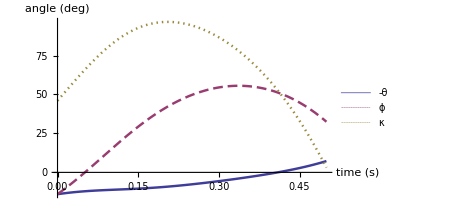

```mathematica
Plot[Evaluate[(180. {-q[1],q[2],q[2]-q[3]})/π/.trajectory],{t,0,0.5},PlotStyle->{{Thickness[0.005]},{Thickness[0.005],Dashing[{0.02,0.01}]},{Thickness[0.005],Dashing[{0.003,0.008}]}},AxesLabel->{"time (s)","angle (deg)"},PlotLegends->{"-θ","ϕ","κ"}]
```

Here is a plot of the segment angles, defined as positive in the ccw direction, measured from the vertical. This is how the segments are defined in Dynamics Workbench.

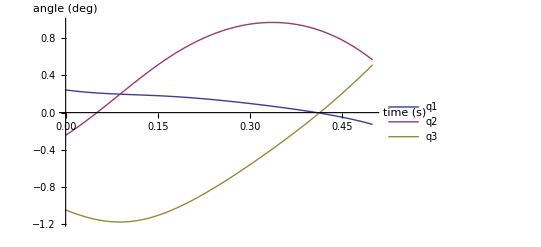

```mathematica
Plot[Evaluate[{q[1],q[2],q[3]}/.trajectory],{t,0,0.5},PlotLegends->{"q1","q2","q3"},AxesLabel->{"time (s)","angle (deg)"}]
```

### Test of energy conservation

Now let's calculate the total energy during the swing cycle, to verify that the Dyamics Workbench model conserves energy. Looking at the axes on the plot, it is evident that energy is conserved within machine precision

```mathematica
KE=1/2 Mass[a] VelCOM[a].VelCOM[a]+1/2 Mass[b] VelCOM[b].VelCOM[b]+1/2 Mass[c] VelCOM[c].VelCOM[c]+1/2 Inertia[a].AngVel[a].AngVel[a]+1/2 Inertia[b].AngVel[b].AngVel[b]+1/2 Inertia[c].AngVel[c].AngVel[c];
PE = -(Mass[a] PosCOM[a].grav+Mass[b] PosCOM[b].grav+Mass[c] PosCOM[c].grav);
```

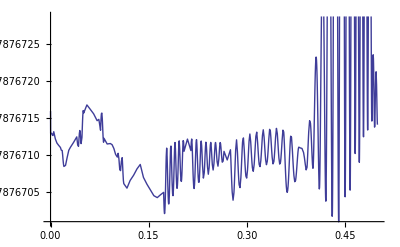

```mathematica
Plot[Evaluate[PE+KE//.constants/.trajectory],{t,0,0.5}]
```

### Exporting code to Matlab

Equations of motion can be automatically exported into a Matlab state-derivative function, compatible with ode45. The command below will write the equations of motion in eom to the file specified. Note that parameters are treated as uninitialized variables, and need to be given values before the function can be executed.

Additional symbolic expressions can also be exported with the equations of motion. These are listed with the option Expressions, each paired with the name of the variable to be created in Matlab.

```mathematica
ExportEOM[eom,OutputFile->"fballwalk.m",Expressions->{{KE,"kineticEnergy"},{PE,"gravPotentialEnergy"}}]
```

Opening file "fballwalk.m"

Current directory: /Users/artkuo

Closing file "fballwalk.m"

## Sample low level operations

#### Cross products

```mathematica
a[1]×b[1]
```

pkgV[{-Sin[qt[1][t]-qt[2][t]],b,3}]

#### Dot products

```mathematica
a[1].c[2]
```

Sin[qt[1][t]-qt[3][t]]

#### Here's a dyadic

```mathematica
r=a[1]**a[2]
```

PV[{PV[{1,a,1}],a,2}]

#### And you can use it like this:

```mathematica
r.b[1]
```

PV[{Cos[qt[1][t]-qt[2][t]],a,2}]

#### Time derivatives of vectors

```mathematica
Dt[3 a[1]×b[1],t]
```

PV[{-3 Cos[qt[1][t]-qt[2][t]] (qt[1]'[t]-qt[2]'[t]),b,3}]